```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"./modelFiles/SMS-stop_FA/SMS-stop_FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
processGGtt =  { V[4],V[4]} -> {-F[9], F[9]};
tops = CreateTopologies[1, 2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
allDiags = InsertFields[tops,processGGtt, InsertionLevel-> {Particles},ExcludeParticles->{F[12],V[1],V[2],V[3]},LastSelections->{S[4]}];
```

generic model {Lorentz} initialized

classes model {./modelFiles/SMS-stop_FA/SMS-stop_FA} initialized

in total: 13 Particles insertions

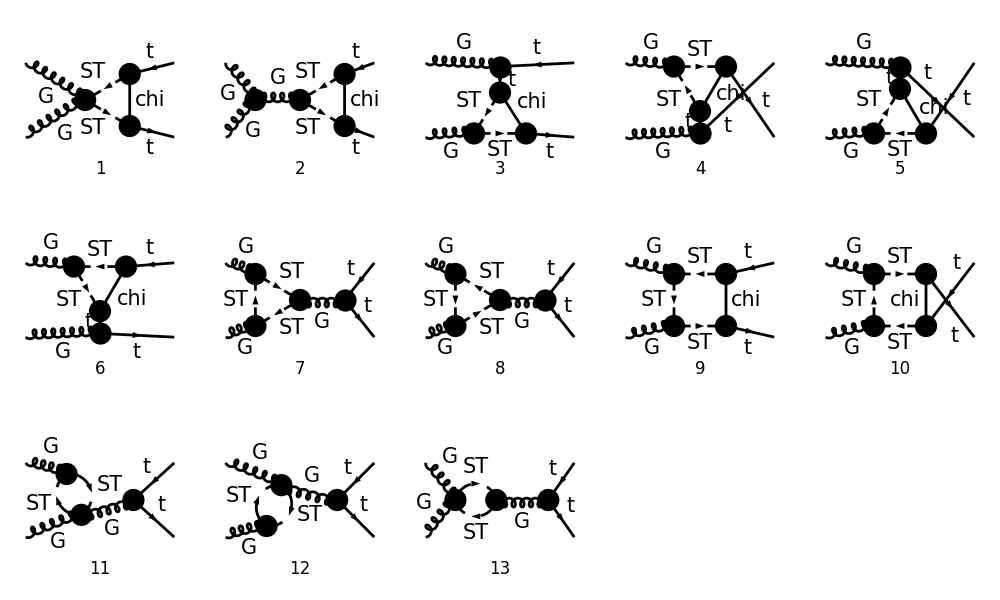

```mathematica
Paint[allDiags,ColumnsXRows->{5,3},ImageSize->{ 1000,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

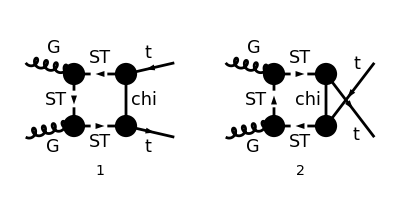

```mathematica
diags=DiagramExtract[allDiags,{9,10}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{400,200},Numbering->Simple];
```

```mathematica
(* Set Truncated->True to remove external fields  *)
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->False,TransversePolarizationVectors->{p1,p2},DropSumOver->True,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 2 Particles amplitudes

(4 π aS (p2+2 q)^ν T_Col5Col3^Glu1 T_Col4Col5^Glu2 (k1+k2-p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(γ·(k2-p2-q)+mChi).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((p2+q)^2-mST^2).((-k2+p2+q)^2-mChi^2).((-k1-k2+p2+q)^2-mST^2))+(4 π aS (p2+2 q)^ν T_Col5Col3^Glu2 T_Col4Col5^Glu1 (k1+k2-p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(γ·(-k1+p2+q)+mChi).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((p2+q)^2-mST^2).((-k1+p2+q)^2-mChi^2).((-k1-k2+p2+q)^2-mST^2))

```mathematica
amp[0]=FCRerouteMomenta[amp[0],{p1,p2},{k1,k2}]
```

(4 π aS (p1-2 q)^μ (p2+2 q)^ν T_Col5Col3^Glu2 T_Col4Col5^Glu1 (-ⅈ yDM (γ̄)^7).(γ·(-k1+p2+q)+mChi).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((p2+q)^2-mST^2).((-k1+p2+q)^2-mChi^2).((q-p1)^2-mST^2))+(4 π aS (p1-2 q)^μ (p2+2 q)^ν T_Col5Col3^Glu1 T_Col4Col5^Glu2 (-ⅈ yDM (γ̄)^7).(γ·(k2-p2-q)+mChi).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((p2+q)^2-mST^2).((-k2+p2+q)^2-mChi^2).((q-p1)^2-mST^2))

```mathematica
PT =1/2( MTD[μ,ν]-FVD[p1,ν]FVD[p2,μ]/ScalarProduct[p1,p2]);
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,k1,k2,0,0,MT,MT];
```

```mathematica
amp[1]=(Contract[PT SUNSimplify[FCTraceFactor[ amp[0]]]]/.{u-> 2 MT^2 -s-t})//Simplify
```

(8 π aS yDM^2 (q^2 s-2 (p1·q) (p2·q)) (((T^Glu1 T^Glu2)_Col4Col3 (γ̄)^7.(mChi-γ·(k1-p2-q)).(γ̄)^6)/((q^2-mST^2).((p2+q)^2-mST^2).((-k1+p2+q)^2-mChi^2).((q-p1)^2-mST^2))+((T^Glu2 T^Glu1)_Col4Col3 (γ̄)^7.(γ·(k2-p2-q)+mChi).(γ̄)^6)/((q^2-mST^2).((p2+q)^2-mST^2).((-k2+p2+q)^2-mChi^2).((q-p1)^2-mST^2))))/s

```mathematica
amp[2]=FullSimplify[DiracSimplify[amp[1]]]
```

(8 π aS yDM^2 (2 (p1·q) (p2·q)-q^2 s) (((T^Glu1 T^Glu2)_Col4Col3 ((γ·k1).(γ̄)^6-(γ·p2).(γ̄)^6-(γ·q).(γ̄)^6))/((q^2-mST^2).((p2+q)^2-mST^2).((k1-p2-q)^2-mChi^2).((p1-q)^2-mST^2))+((T^Glu2 T^Glu1)_Col4Col3 (-(γ·k2).(γ̄)^6+(γ·p2).(γ̄)^6+(γ·q).(γ̄)^6))/((q^2-mST^2).((p2+q)^2-mST^2).((k2-p2-q)^2-mChi^2).((p1-q)^2-mST^2))))/s

```mathematica
amp[3]=TID[amp[2],q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify
```

-1/s 4 ⅈ aS π^3 yDM^2 (2 s D_0(MT^2,0,0,3 MT^2+s-t-u,2 MT^2-u,s,mChi^2,mST^2,mST^2,mST^2) (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mST^2+2 s (γ·k1).(γ̄)^6 D_1(MT^2,2 MT^2-u,0,s,0,3 MT^2+s-t-u,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2+2 s (γ·p2).(γ̄)^6 D_2(MT^2,2 MT^2-u,0,s,0,3 MT^2+s-t-u,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2-2 s (-(γ·(p1+p2))).(γ̄)^6 D_3(MT^2,2 MT^2-u,0,s,0,3 MT^2+s-t-u,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2-2 s D_0(MT^2,0,0,3 MT^2+s-t-u,2 MT^2-t,s,mChi^2,mST^2,mST^2,mST^2) (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 mST^2-2 s (γ·k2).(γ̄)^6 D_1(MT^2,2 MT^2-t,0,s,0,3 MT^2+s-t-u,mST^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col4Col3 mST^2-2 s (γ·p2).(γ̄)^6 D_2(MT^2,2 MT^2-t,0,s,0,3 MT^2+s-t-u,mST^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col4Col3 mST^2+2 s (-(γ·(p1+p2))).(γ̄)^6 D_3(MT^2,2 MT^2-t,0,s,0,3 MT^2+s-t-u,mST^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col4Col3 mST^2+B_0(2 MT^2-u,mChi^2,mST^2) ((γ·k1).(γ̄)^6-(γ·p2).(γ̄)^6) (T^Glu1 T^Glu2)_Col4Col3-(-(γ·(k1-p2))).(γ̄)^6 B_1(2 MT^2-u,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col4Col3+2 (γ·p2).(γ̄)^6 C_00(MT^2,3 MT^2+s-t-u,s,mST^2,mChi^2,mST^2) ((T^Glu1 T^Glu2)_Col4Col3-(T^Glu2 T^Glu1)_Col4Col3)-s (-(γ·(p1+p2))).(γ̄)^6 C_22(MT^2,3 MT^2+s-t-u,s,mST^2,mChi^2,mST^2) ((T^Glu1 T^Glu2)_Col4Col3-(T^Glu2 T^Glu1)_Col4Col3)-B_0(2 MT^2-t,mChi^2,mST^2) ((γ·k2).(γ̄)^6-(γ·p2).(γ̄)^6) (T^Glu2 T^Glu1)_Col4Col3+(-(γ·(k2-p2))).(γ̄)^6 B_1(2 MT^2-t,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col4Col3+2 s C_0(MT^2,s,3 MT^2+s-t-u,mChi^2,mST^2,mST^2) ((γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-(γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)+B_1(MT^2,mChi^2,mST^2) ((γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-(γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)+s C_2(MT^2,3 MT^2+s-t-u,s,mST^2,mChi^2,mST^2) ((γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-2 (-(γ·(p1+p2))).(γ̄)^6 ((T^Glu1 T^Glu2)_Col4Col3-(T^Glu2 T^Glu1)_Col4Col3)-(γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)-C_11(MT^2,3 MT^2+s-t-u,s,mST^2,mChi^2,mST^2) ((MT^2-u) (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+(t-MT^2) (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)-C_1(MT^2,3 MT^2+s-t-u,s,mST^2,mChi^2,mST^2) ((MT^2-2 s-u) (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+(-MT^2+2 s+t) (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)+C_12(MT^2,3 MT^2+s-t-u,s,mST^2,mChi^2,mST^2) (s (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-s (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3+(-(γ·(p1+p2))).(γ̄)^6 ((MT^2-u) (T^Glu1 T^Glu2)_Col4Col3+(t-MT^2) (T^Glu2 T^Glu1)_Col4Col3)))

```mathematica
(* Make sure there are no divergences *)
UVpart = DiracSimplify[PaXEvaluateUV[amp[3]]]
```

0

```mathematica
amp[5]=(amp[3]/.{u-> 2 MT^2 -s-t})//FullSimplify
```

-1/s 4 ⅈ aS π^3 yDM^2 (2 s D_0(MT^2,0,0,MT^2+2 s,s+t,s,mChi^2,mST^2,mST^2,mST^2) (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mST^2+2 s (γ·k1).(γ̄)^6 D_1(MT^2,s+t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2+2 s (γ·p2).(γ̄)^6 D_2(MT^2,s+t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2-2 s (-(γ·(p1+p2))).(γ̄)^6 D_3(MT^2,s+t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu1 T^Glu2)_Col4Col3 mST^2-2 s D_0(MT^2,0,0,MT^2+2 s,2 MT^2-t,s,mChi^2,mST^2,mST^2,mST^2) (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3 mST^2-2 s (γ·k2).(γ̄)^6 D_1(MT^2,2 MT^2-t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col4Col3 mST^2-2 s (γ·p2).(γ̄)^6 D_2(MT^2,2 MT^2-t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col4Col3 mST^2+2 s (-(γ·(p1+p2))).(γ̄)^6 D_3(MT^2,2 MT^2-t,0,s,0,MT^2+2 s,mST^2,mChi^2,mST^2,mST^2) (T^Glu2 T^Glu1)_Col4Col3 mST^2+B_0(s+t,mChi^2,mST^2) ((γ·k1).(γ̄)^6-(γ·p2).(γ̄)^6) (T^Glu1 T^Glu2)_Col4Col3-(-(γ·(k1-p2))).(γ̄)^6 B_1(s+t,mST^2,mChi^2) (T^Glu1 T^Glu2)_Col4Col3+2 (γ·p2).(γ̄)^6 C_00(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) ((T^Glu1 T^Glu2)_Col4Col3-(T^Glu2 T^Glu1)_Col4Col3)+B_0(2 MT^2-t,mChi^2,mST^2) ((γ·p2).(γ̄)^6-(γ·k2).(γ̄)^6) (T^Glu2 T^Glu1)_Col4Col3+(-(γ·(k2-p2))).(γ̄)^6 B_1(2 MT^2-t,mST^2,mChi^2) (T^Glu2 T^Glu1)_Col4Col3+s (-(γ·(p1+p2))).(γ̄)^6 C_22(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) ((T^Glu2 T^Glu1)_Col4Col3-(T^Glu1 T^Glu2)_Col4Col3)+2 s C_0(MT^2,s,MT^2+2 s,mChi^2,mST^2,mST^2) ((γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-(γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)+B_1(MT^2,mChi^2,mST^2) ((γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-(γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)-C_11(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) ((-MT^2+s+t) (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+(t-MT^2) (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)-C_1(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) ((-MT^2+2 s+t) (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3-(MT^2+s-t) (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)+s C_2(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (((γ·k1).(γ̄)^6-2 (-(γ·(p1+p2))).(γ̄)^6) (T^Glu1 T^Glu2)_Col4Col3-((γ·k2).(γ̄)^6-2 (-(γ·(p1+p2))).(γ̄)^6) (T^Glu2 T^Glu1)_Col4Col3)+C_12(MT^2,MT^2+2 s,s,mST^2,mChi^2,mST^2) (s (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-s (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3+(-(γ·(p1+p2))).(γ̄)^6 ((-MT^2+s+t) (T^Glu1 T^Glu2)_Col4Col3+(t-MT^2) (T^Glu2 T^Glu1)_Col4Col3)))

#### EFT Limit (s,t,u,MT →0)

```mathematica
FullSimplify[Expand[PaXEvaluate[amp[5],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries-> {{s,0,0},{MT,0,0},{t,0,0},{u,0,0}}]],Assumptions->{mST>0,mChi>0,μ>0}]
```

1/(144 ε (mChi-mST)^4 (mChi+mST)^4 π s)ⅈ aS yDM^2 (9 ε (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^8-18 ε ℽ (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^8+18 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^8-36 ε (γ·p2).(γ̄)^6 log(mChi/mST) (T^Glu1 T^Glu2)_Col4Col3 mChi^8+18 ε (γ·p2).(γ̄)^6 log((4 π μ^2)/mST^2) (T^Glu1 T^Glu2)_Col4Col3 mChi^8-54 ε mST^2 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^6+72 ε ℽ mST^2 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^6-72 mST^2 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^6+29 ε s (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^6+38 ε s (γ·(p1+p2)).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^6+144 ε mST^2 (γ·p2).(γ̄)^6 log(mChi/mST) (T^Glu1 T^Glu2)_Col4Col3 mChi^6-12 ε s (γ·p2).(γ̄)^6 log(mChi/mST) (T^Glu1 T^Glu2)_Col4Col3 mChi^6-48 ε s (γ·(p1+p2)).(γ̄)^6 log(mChi/mST) (T^Glu1 T^Glu2)_Col4Col3 mChi^6-72 ε mST^2 (γ·p2).(γ̄)^6 log((4 π μ^2)/mST^2) (T^Glu1 T^Glu2)_Col4Col3 mChi^6+108 ε mST^4 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^4-108 ε ℽ mST^4 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^4+108 mST^4 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^4-36 ε mST^2 s (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^4-81 ε mST^2 s (γ·(p1+p2)).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^4-180 ε mST^4 (γ·p2).(γ̄)^6 log(mChi/mST) (T^Glu1 T^Glu2)_Col4Col3 mChi^4-72 ε mST^2 s (γ·p2).(γ̄)^6 log(mChi/mST) (T^Glu1 T^Glu2)_Col4Col3 mChi^4+36 ε mST^2 s (γ·(p1+p2)).(γ̄)^6 log(mChi/mST) (T^Glu1 T^Glu2)_Col4Col3 mChi^4+108 ε mST^4 (γ·p2).(γ̄)^6 log((4 π μ^2)/mST^2) (T^Glu1 T^Glu2)_Col4Col3 mChi^4-90 ε mST^6 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^2+72 ε ℽ mST^6 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^2-72 mST^6 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^2-9 ε mST^4 s (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^2+54 ε mST^4 s (γ·(p1+p2)).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3 mChi^2+72 ε mST^6 (γ·p2).(γ̄)^6 log(mChi/mST) (T^Glu1 T^Glu2)_Col4Col3 mChi^2+72 ε mST^4 s (γ·p2).(γ̄)^6 log(mChi/mST) (T^Glu1 T^Glu2)_Col4Col3 mChi^2-72 ε mST^6 (γ·p2).(γ̄)^6 log((4 π μ^2)/mST^2) (T^Glu1 T^Glu2)_Col4Col3 mChi^2+27 ε mST^8 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-18 ε ℽ mST^8 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+18 mST^8 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+16 ε mST^6 s (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-11 ε mST^6 s (γ·(p1+p2)).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-3 (γ·(k1-p2)).(γ̄)^6 (24 ε mChi^2 (2 mST^2-3 mChi^2) log(2) mST^4+(mChi-mST) (mChi+mST) (3 (mChi-mST)^2 (mChi+mST)^2 ((ε (-1+2 ℽ)-2) mChi^2+((3-2 ℽ) ε+2) mST^2)-2 ε (mChi^4-5 mST^2 mChi^2-2 mST^4) s)-12 ε (log(2/mChi) mChi^8+4 mST^2 log(mChi/2) mChi^6+mST^4 (-log(mChi^5 mST) mChi^2+2 s log(mChi/mST)+2 mST^2 log(mChi mST)) mChi^2+mST^8 log(2/mST))-6 ε (mChi^2-mST^2)^4 log(π μ^2)) (T^Glu1 T^Glu2)_Col4Col3+18 ε mST^8 (γ·p2).(γ̄)^6 log((4 π μ^2)/mST^2) (T^Glu1 T^Glu2)_Col4Col3+9 (γ·k1).(γ̄)^6 ((ε (-1+2 ℽ)-2) mChi^8+(mST^2 (2 (3-4 ℽ+log(256)) ε+8)-13 ε s) mChi^6+4 mST^2 (3 (ε (-1+ℽ)-1) mST^2+5 ε s) mChi^4+(2 mST^6 ((5-4 ℽ+log(256)) ε+4)-7 ε mST^4 s) mChi^2+4 ε ((3 s-4 mST^2) mChi^4+(5 mST^4+2 s mST^2) mChi^2-2 mST^4 (mST^2+s)) log(mChi/mST) mChi^2+mST^8 (ε (-3+2 ℽ-4 log(2))-2)-2 ε (2 log((2 mST)/mChi) mChi^8+6 mST^4 log((4 π μ^2)/mST^2) mChi^4+(mChi^8-4 mST^2 mChi^6-4 mST^6 mChi^2+mST^8) log((π μ^2)/mST^2))) (T^Glu1 T^Glu2)_Col4Col3-(9 ε (γ·p2).(γ̄)^6 mChi^8-18 ε ℽ (γ·p2).(γ̄)^6 mChi^8+18 (γ·p2).(γ̄)^6 mChi^8-18 ε (γ·p2).(γ̄)^6 log((4 mChi^2 π μ^2)/mST^4) mChi^8+36 ε (γ·p2).(γ̄)^6 log((π μ^2)/mST^2) mChi^8+72 ε (γ·p2).(γ̄)^6 log(2) mChi^8-54 ε mST^2 (γ·p2).(γ̄)^6 mChi^6+72 ε ℽ mST^2 (γ·p2).(γ̄)^6 mChi^6-72 mST^2 (γ·p2).(γ̄)^6 mChi^6+11 ε s (γ·p2).(γ̄)^6 mChi^6+44 ε s (γ·(p1+p2)).(γ̄)^6 mChi^6-12 ε s (γ·p2).(γ̄)^6 log(mChi/mST) mChi^6-48 ε s (γ·(p1+p2)).(γ̄)^6 log(mChi/mST) mChi^6+72 ε mST^2 (γ·p2).(γ̄)^6 log((4 mChi^2 π μ^2)/mST^4) mChi^6-144 ε mST^2 (γ·p2).(γ̄)^6 log((π μ^2)/mST^2) mChi^6-288 ε mST^2 (γ·p2).(γ̄)^6 log(2) mChi^6+108 ε mST^4 (γ·p2).(γ̄)^6 mChi^4-108 ε ℽ mST^4 (γ·p2).(γ̄)^6 mChi^4+108 mST^4 (γ·p2).(γ̄)^6 mChi^4-18 ε mST^2 s (γ·p2).(γ̄)^6 mChi^4-72 ε mST^2 s (γ·(p1+p2)).(γ̄)^6 mChi^4-180 ε mST^4 (γ·p2).(γ̄)^6 log(mChi/mST) mChi^4+216 ε mST^4 (γ·p2).(γ̄)^6 log((π μ^2)/mST^2) mChi^4+432 ε mST^4 (γ·p2).(γ̄)^6 log(2) mChi^4-90 ε mST^6 (γ·p2).(γ̄)^6 mChi^2+72 ε ℽ mST^6 (γ·p2).(γ̄)^6 mChi^2-72 mST^6 (γ·p2).(γ̄)^6 mChi^2+9 ε mST^4 s (γ·p2).(γ̄)^6 mChi^2+36 ε mST^4 s (γ·(p1+p2)).(γ̄)^6 mChi^2+72 ε mST^6 (γ·p2).(γ̄)^6 log((4 mChi π μ^2)/mST^3) mChi^2-144 ε mST^6 (γ·p2).(γ̄)^6 log((π μ^2)/mST^2) mChi^2-288 ε mST^6 (γ·p2).(γ̄)^6 log(2) mChi^2+27 ε mST^8 (γ·p2).(γ̄)^6-18 ε ℽ mST^8 (γ·p2).(γ̄)^6+18 mST^8 (γ·p2).(γ̄)^6-2 ε mST^6 s (γ·p2).(γ̄)^6-8 ε mST^6 s (γ·(p1+p2)).(γ̄)^6-9 (γ·(k2-p2)).(γ̄)^6 (4 ε (mChi^2-2 mST^2) log(mChi/2) mChi^6-16 ε mST^4 log(2/mChi) mChi^4+(mChi-mST)^3 (mChi+mST)^3 ((2 ℽ ε-ε-2) mChi^2+(-2 ℽ ε+3 ε+2) mST^2)+2 ε (-log(ⅈ μ) mChi^8+4 mST^2 log((2 ⅈ μ)/mChi) mChi^6+2 mST^4 log((mChi mST)/4) mChi^4-6 mST^4 log(ⅈ μ) mChi^4+4 mST^6 log((2 ⅈ μ)/mChi) mChi^2+2 mST^6 (mST^2-2 mChi^2) log(mST/2)-mST^8 log(ⅈ μ)-(mChi^2-mST^2)^4 log(-ⅈ π μ)))+36 ε mST^8 (γ·p2).(γ̄)^6 log((π μ^2)/mST^2)-18 ε mST^4 (6 mChi^4+mST^4) (γ·p2).(γ̄)^6 log((4 π μ^2)/mST^2)+3 (γ·k2).(γ̄)^6 ((mChi-mST) (mChi+mST) (3 (mChi-mST)^2 ((ε (-1+2 ℽ)-2) mChi^2+((3-2 ℽ) ε+2) mST^2) (mChi+mST)^2+ε (-37 mChi^4+11 mST^2 mChi^2-4 mST^4) s)+6 ε (log(μ^2/mST^2) mST^8-4 mChi^2 log((mChi μ^2)/mST^3) mST^6+6 mChi^4 log(μ^2/mST^2) mST^4+2 mChi^4 (5 mST^4+2 s mST^2+3 mChi^2 s) log(mChi/mST)+(mChi^8-4 mChi^6 mST^2) log((mChi^2 μ^2)/mST^4)-2 (mChi^2-mST^2)^4 log((2 π^2 μ^2)/mST^2)+3 (mChi^2-mST^2)^4 log(π)))+72 ε mST^8 (γ·p2).(γ̄)^6 log(2)) (T^Glu2 T^Glu1)_Col4Col3)

```mathematica
Limit[%,mChi-> mST]
```

1/(s ε)aS yDM^2 ((-ⅈ mST^4 ε ((γ·(k1-p2)).(γ̄)^6 (-2 log(1/mST)-4 log(mST)-2 log(mST^2)+log(mST^6)) (T^Glu1 T^Glu2)_Col4Col3+(γ·(k2-p2)).(γ̄)^6 (4 log(1/mST)+2 log(mST)-log(mST^2)+4 log(ⅈ μ)-4 log((2 ⅈ μ)/mST)+log(16)) (T^Glu2 T^Glu1)_Col4Col3)) ∞)

```mathematica
Factor[Expand[%43]]
```

1/(96 π mST^2)ⅈ aS yDM^2 (7 (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3-7 (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3-5 (γ·p1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+4 (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3-4 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3+5 (γ·p2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)

```mathematica
Collect[Expand[%43],DiracGamma[x_,D]]
```

(7 ⅈ aS yDM^2 (γ·k1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)/(96 π mST^2)-(7 ⅈ aS yDM^2 (γ·k2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(96 π mST^2)-(5 ⅈ aS yDM^2 (γ·p1).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)/(96 π mST^2)+(ⅈ aS yDM^2 (γ·p1).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(24 π mST^2)-(ⅈ aS yDM^2 (γ·p2).(γ̄)^6 (T^Glu1 T^Glu2)_Col4Col3)/(24 π mST^2)+(5 ⅈ aS yDM^2 (γ·p2).(γ̄)^6 (T^Glu2 T^Glu1)_Col4Col3)/(96 π mST^2)

```mathematica
Collect[Expand[%43]/.{DiracGamma[Momentum[x_,D],D].DiracGamma[6]-> GS[x] Subscript[P, L]},{GS[p1],GS[p2],GS[k1],GS[k2]},Simplify]
```

(7 ⅈ aS yDM^2 P_L γ̄·OverBar[k1] (T^Glu1 T^Glu2)_Col4Col3)/(96 π mST^2)-(7 ⅈ aS yDM^2 P_L γ̄·OverBar[k2] (T^Glu2 T^Glu1)_Col4Col3)/(96 π mST^2)-(ⅈ aS yDM^2 P_L γ̄·OverBar[p1] (5 (T^Glu1 T^Glu2)_Col4Col3-4 (T^Glu2 T^Glu1)_Col4Col3))/(96 π mST^2)-(ⅈ aS yDM^2 P_L γ̄·OverBar[p2] (4 (T^Glu1 T^Glu2)_Col4Col3-5 (T^Glu2 T^Glu1)_Col4Col3))/(96 π mST^2)